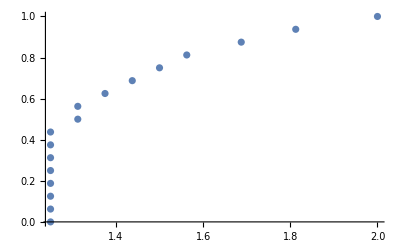

```mathematica
a={{1.250000,0.000000},{1.250000,0.062500},{1.250000,0.125000},{1.250000,0.187500},{1.250000,0.250000},{1.250000,0.312500},{1.250000,0.375000},{1.250000,0.437500},{1.312500,0.500000},{1.312500,0.562500},{1.375000,0.625000},{1.437500,0.687500},{1.500000,0.750000},{1.562500,0.812500},{1.687500,0.875000},{1.812500,0.937500},{2.000000,1.000000}};
ListPlot[a]
```

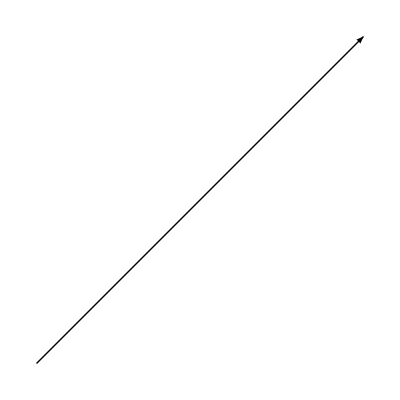

```mathematica
Graphics[Arrow[{{1,1},{2,2}}]]
```

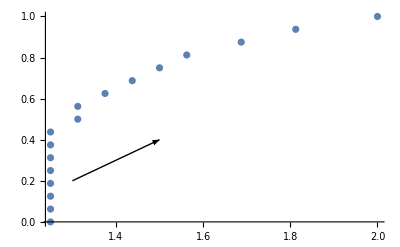

```mathematica
ListPlot[a, Epilog->{Arrow[{{1.3,0.2},{1.5,0.4}}]}]
```

```mathematica
b={{1.3,0.2},{1.5,0.4}};
ListPlot[a, Epilog->{Arrow[b]}]
```

-Graphics-

```mathematica
myarrows=Table[Arrow[{{0,0,0},{1/i,(1-i)/5,(1-i)/5}}],{i,1,10}];

Graphics3D[myarrows]
```

-Graphics3D-

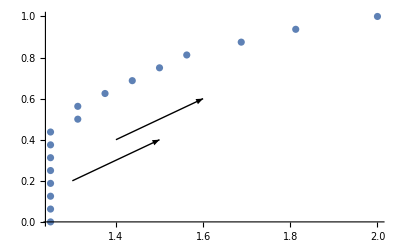

```mathematica
b={{1.3,0.2},{1.5,0.4}};
c={{1.4,0.4},{1.6,0.6}};
ListPlot[a, Epilog->{Arrow[b],Arrow[c]}]
```

```mathematica
b={{1.3,0.2},{1.5,0.4}};
c={{1.4,0.4},{1.6,0.6}};
d={Arrow[b],Arrow[c]};
ListPlot[a, Epilog->d]
```

-Graphics-

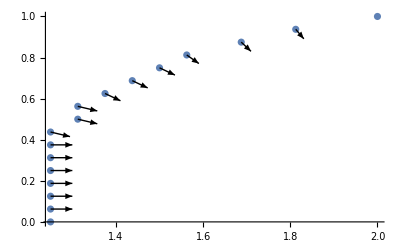

```mathematica
e={Arrow[{{1.250000,0.062500},{1.250000+0.05*Sin[1.570796],0.062500+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.125000},{1.250000+0.05*Sin[1.570796],0.125000+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.187500},{1.250000+0.05*Sin[1.570796],0.187500+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.250000},{1.250000+0.05*Sin[1.570796],0.250000+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.312500},{1.250000+0.05*Sin[1.570796],0.312500+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.375000},{1.250000+0.05*Sin[1.570796],0.375000+0.05*Cos[1.570796]}}],
Arrow[{{1.250000,0.437500},{1.250000+0.05*Sin[2.034444],0.437500+0.05*Cos[2.034444]}}],
Arrow[{{1.312500,0.500000},{1.312500+0.05*Sin[2.034444],0.500000+0.05*Cos[2.034444]}}],
Arrow[{{1.312500,0.562500},{1.312500+0.05*Sin[2.034444],0.562500+0.05*Cos[2.034444]}}],
Arrow[{{1.375000,0.625000},{1.375000+0.05*Sin[2.356194],0.625000+0.05*Cos[2.356194]}}],
Arrow[{{1.437500,0.687500},{1.437500+0.05*Sin[2.356194],0.687500+0.05*Cos[2.356194]}}],
Arrow[{{1.500000,0.750000},{1.500000+0.05*Sin[2.356194],0.750000+0.05*Cos[2.356194]}}],
Arrow[{{1.562500,0.812500},{1.562500+0.05*Sin[2.553590],0.812500+0.05*Cos[2.553590]}}],
Arrow[{{1.687500,0.875000},{1.687500+0.05*Sin[2.677945],0.875000+0.05*Cos[2.677945]}}],
Arrow[{{1.812500,0.937500},{1.812500+0.05*Sin[2.761086],0.937500+0.05*Cos[2.761086]}}]};
ListPlot[a, Epilog->e]
```

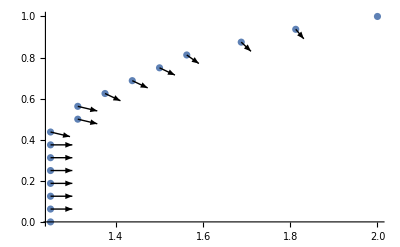

```mathematica
e2={Arrow[{{1.250000,0.062500},{1.300000,0.062500}}],
Arrow[{{1.250000,0.125000},{1.300000,0.125000}}],
Arrow[{{1.250000,0.187500},{1.300000,0.187500}}],
Arrow[{{1.250000,0.250000},{1.300000,0.250000}}],
Arrow[{{1.250000,0.312500},{1.300000,0.312500}}],
Arrow[{{1.250000,0.375000},{1.300000,0.375000}}],
Arrow[{{1.250000,0.437500},{1.294721,0.415139}}],
Arrow[{{1.312500,0.500000},{1.357221,0.477639}}],
Arrow[{{1.312500,0.562500},{1.357221,0.540139}}],
Arrow[{{1.375000,0.625000},{1.410355,0.589645}}],
Arrow[{{1.437500,0.687500},{1.472855,0.652145}}],
Arrow[{{1.500000,0.750000},{1.535355,0.714645}}],
Arrow[{{1.562500,0.812500},{1.590235,0.770897}}],
Arrow[{{1.687500,0.875000},{1.709861,0.830279}}],
Arrow[{{1.812500,0.937500},{1.831070,0.891076}}]};
ListPlot[a, Epilog->e2]
```

```mathematica
e3={Arrow[{{1.250000,0.062500},{1.300000,0.062500}}],Arrow[{{1.250000,0.125000},{1.300000,0.125000}}],Arrow[{{1.250000,0.187500},{1.300000,0.187500}}],Arrow[{{1.250000,0.250000},{1.300000,0.250000}}],Arrow[{{1.250000,0.312500},{1.300000,0.312500}}],Arrow[{{1.250000,0.375000},{1.300000,0.375000}}],Arrow[{{1.250000,0.437500},{1.294721,0.415139}}],Arrow[{{1.312500,0.500000},{1.357221,0.477639}}],Arrow[{{1.312500,0.562500},{1.357221,0.540139}}],Arrow[{{1.375000,0.625000},{1.410355,0.589645}}],Arrow[{{1.437500,0.687500},{1.472855,0.652145}}],Arrow[{{1.500000,0.750000},{1.535355,0.714645}}],Arrow[{{1.562500,0.812500},{1.590235,0.770897}}],Arrow[{{1.687500,0.875000},{1.709861,0.830279}}],Arrow[{{1.812500,0.937500},{1.831070,0.891076}}]};
ListPlot[a, Epilog->e3]
```

-Graphics-

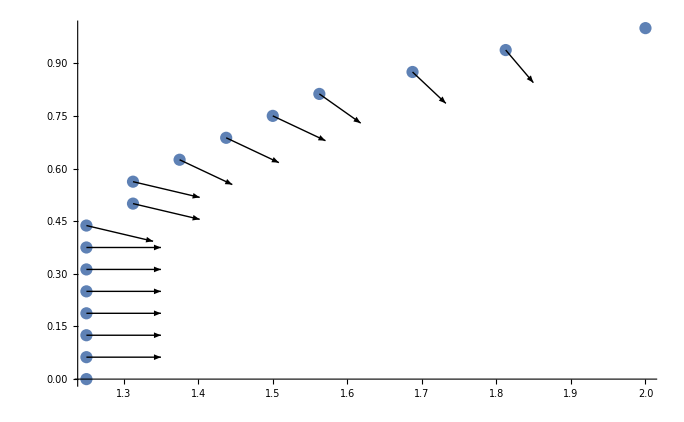

```mathematica
e4={Arrow[{{1.250000,0.062500},{1.350000,0.062500}}],Arrow[{{1.250000,0.125000},{1.350000,0.125000}}],Arrow[{{1.250000,0.187500},{1.350000,0.187500}}],Arrow[{{1.250000,0.250000},{1.350000,0.250000}}],Arrow[{{1.250000,0.312500},{1.350000,0.312500}}],Arrow[{{1.250000,0.375000},{1.350000,0.375000}}],Arrow[{{1.250000,0.437500},{1.339443,0.392779}}],Arrow[{{1.312500,0.500000},{1.401943,0.455279}}],Arrow[{{1.312500,0.562500},{1.401943,0.517779}}],Arrow[{{1.375000,0.625000},{1.445711,0.554289}}],Arrow[{{1.437500,0.687500},{1.508211,0.616789}}],Arrow[{{1.500000,0.750000},{1.570711,0.679289}}],Arrow[{{1.562500,0.812500},{1.617970,0.729295}}],Arrow[{{1.687500,0.875000},{1.732221,0.785557}}],Arrow[{{1.812500,0.937500},{1.849639,0.844652}}]};
ListPlot[a, Epilog->e4]
```

```mathematica
1.849639-1.812500
```

0.037139

```mathematica
0.844652-0.937500
```

-0.092848

```mathematica
Tan[0.03713900000000003/0.09284800000000004]
```

0.422791

```mathematica
2.761086+0.422790679635473
```

3.18388

```mathematica
2.76+0.380506
```

3.14051

```mathematica
Tan[0.037139/0.092848]
```

0.422791

```mathematica
ArcTan[0.037139/0.092848]
```

0.380505

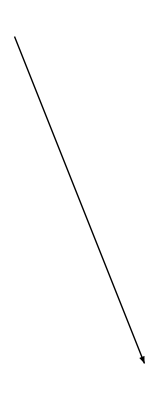

```mathematica
Graphics[Arrow[{{1.812500,0.937500},{1.849639,0.844652}}]]
```

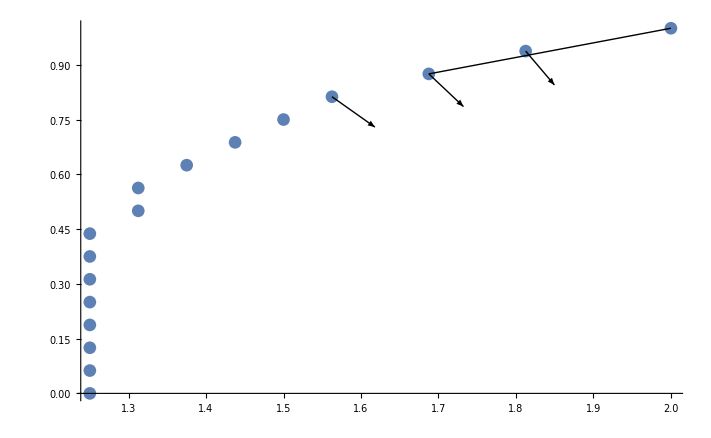

```mathematica
e4={Arrow[{{1.562500,0.812500},{1.617970,0.729295}}],Arrow[{{1.687500,0.875000},{1.732221,0.785557}}],Arrow[{{1.812500,0.937500},{1.849639,0.844652}}]};
f=ListPlot[a, Epilog->{e4,Line[{{1.687500,0.875000},{2.000000,1.000000}}]}]
```

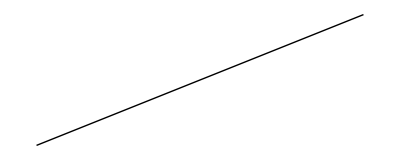

```mathematica
ff=Graphics[Line[{{1.687500,0.875000},{2.000000,1.000000}}]]
```

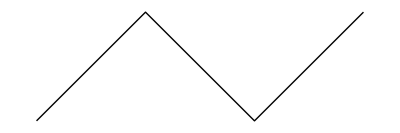

```mathematica
Graphics[Line[{{1,0},{2,1},{3,0},{4,1}}]]
```

```mathematica
ArcTan[(1.0-0.875)/(2.0-1.6875)]
```

0.380506

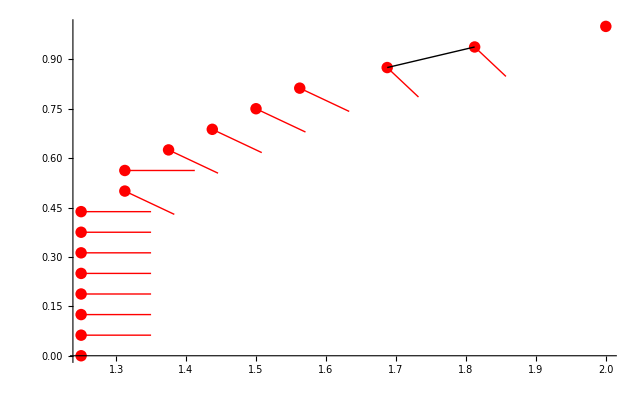

```mathematica
e5={Arrow[{{1.250000,0.062500},{1.350000,0.062500}}],Arrow[{{1.250000,0.125000},{1.350000,0.125000}}],Arrow[{{1.250000,0.187500},{1.350000,0.187500}}],Arrow[{{1.250000,0.250000},{1.350000,0.250000}}],Arrow[{{1.250000,0.312500},{1.350000,0.312500}}],Arrow[{{1.250000,0.375000},{1.350000,0.375000}}],Arrow[{{1.250000,0.437500},{1.350000,0.437500}}],Arrow[{{1.312500,0.500000},{1.383211,0.429289}}],Arrow[{{1.312500,0.562500},{1.412500,0.562500}}],Arrow[{{1.375000,0.625000},{1.445711,0.554289}}],Arrow[{{1.437500,0.687500},{1.508211,0.616789}}],Arrow[{{1.500000,0.750000},{1.570711,0.679289}}],Arrow[{{1.562500,0.812500},{1.633211,0.741789}}],Arrow[{{1.687500,0.875000},{1.732221,0.785557}}],Arrow[{{1.812500,0.937500},{1.857221,0.848057}}]};
ListPlot[a,PlotStyle->Red, Epilog->{{Red,Arrowheads[0],e5},Line[{{1.687500,0.875000},{1.812500,0.937500}}]}]
```

```mathematica
1.8125-1.6875
```

0.125

```mathematica
0.9375-0.875
```

0.0625

```mathematica
1.857221-1.8125
```

0.044721

```mathematica
0.848057-0.9375
```

-0.089443

```mathematica
0.125*0.044721-0.0625*0.089443
```

-6.25×10^-8

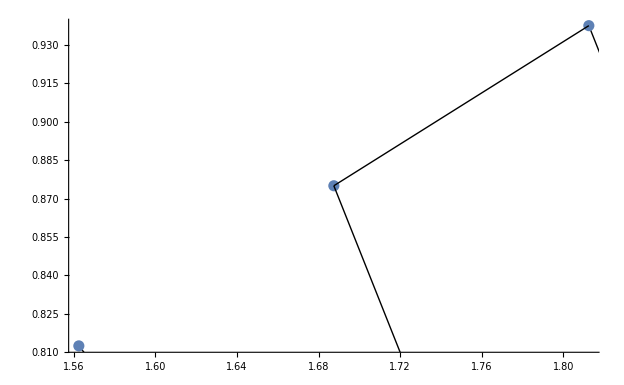

```mathematica
aa={{1.562500,0.812500},{1.687500,0.875000},{1.812500,0.937500}};
ee={Arrow[{{1.562500,0.812500},{1.633211,0.741789}}],Arrow[{{1.687500,0.875000},{1.732221,0.785557}}],Arrow[{{1.812500,0.937500},{1.857221,0.848057}}]};
ListPlot[aa, Epilog->{ee,Line[{{1.687500,0.875000},{1.812500,0.937500}}]}]
```

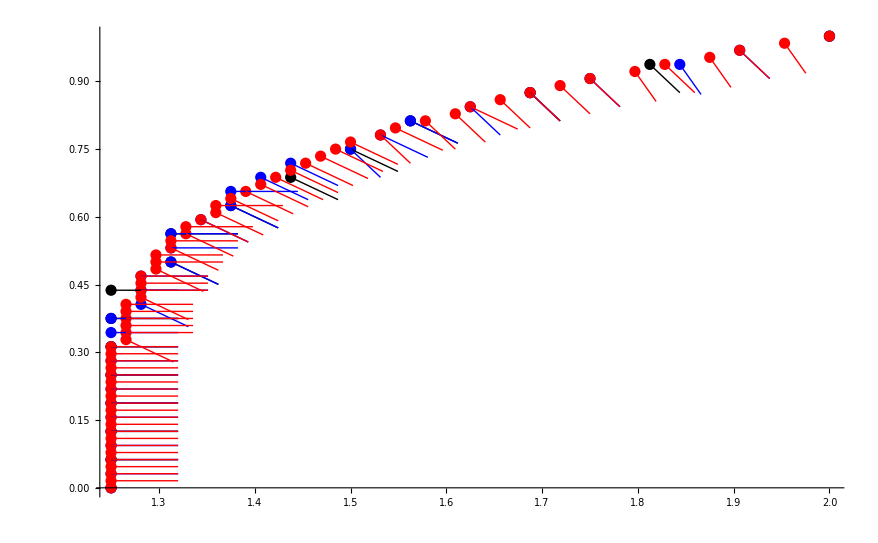

```mathematica
a1={{1.250000,0.000000},{1.250000,0.062500},{1.250000,0.125000},{1.250000,0.187500},{1.250000,0.250000},{1.250000,0.312500},{1.250000,0.375000},{1.250000,0.437500},{1.312500,0.500000},{1.312500,0.562500},{1.375000,0.625000},{1.437500,0.687500},{1.500000,0.750000},{1.562500,0.812500},{1.687500,0.875000},{1.812500,0.937500},{2.000000,1.000000}};
b1={Arrow[{{1.250000,0.062500},{1.320000,0.062500}}],Arrow[{{1.250000,0.125000},{1.320000,0.125000}}],Arrow[{{1.250000,0.187500},{1.320000,0.187500}}],Arrow[{{1.250000,0.250000},{1.320000,0.250000}}],Arrow[{{1.250000,0.312500},{1.320000,0.312500}}],Arrow[{{1.250000,0.375000},{1.320000,0.375000}}],Arrow[{{1.250000,0.437500},{1.320000,0.437500}}],Arrow[{{1.312500,0.500000},{1.361997,0.450503}}],Arrow[{{1.312500,0.562500},{1.382500,0.562500}}],Arrow[{{1.375000,0.625000},{1.424497,0.575503}}],Arrow[{{1.437500,0.687500},{1.486997,0.638003}}],Arrow[{{1.500000,0.750000},{1.549497,0.700503}}],Arrow[{{1.562500,0.812500},{1.611997,0.763003}}],Arrow[{{1.687500,0.875000},{1.718805,0.812390}}],Arrow[{{1.812500,0.937500},{1.843805,0.874890}}]};
a2={{1.250000,0.000000},{1.250000,0.031250},{1.250000,0.062500},{1.250000,0.093750},{1.250000,0.125000},{1.250000,0.156250},{1.250000,0.187500},{1.250000,0.218750},{1.250000,0.250000},{1.250000,0.281250},{1.250000,0.312500},{1.250000,0.343750},{1.250000,0.375000},{1.281250,0.406250},{1.281250,0.437500},{1.281250,0.468750},{1.312500,0.500000},{1.312500,0.531250},{1.312500,0.562500},{1.343750,0.593750},{1.375000,0.625000},{1.375000,0.656250},{1.406250,0.687500},{1.437500,0.718750},{1.500000,0.750000},{1.531250,0.781250},{1.562500,0.812500},{1.625000,0.843750},{1.687500,0.875000},{1.750000,0.906250},{1.843750,0.937500},{1.906250,0.968750},{2.000000,1.000000}};
b2={Arrow[{{1.250000,0.031250},{1.320000,0.031250}}],Arrow[{{1.250000,0.062500},{1.320000,0.062500}}],Arrow[{{1.250000,0.093750},{1.320000,0.093750}}],Arrow[{{1.250000,0.125000},{1.320000,0.125000}}],Arrow[{{1.250000,0.156250},{1.320000,0.156250}}],Arrow[{{1.250000,0.187500},{1.320000,0.187500}}],Arrow[{{1.250000,0.218750},{1.320000,0.218750}}],Arrow[{{1.250000,0.250000},{1.320000,0.250000}}],Arrow[{{1.250000,0.281250},{1.320000,0.281250}}],Arrow[{{1.250000,0.312500},{1.320000,0.312500}}],Arrow[{{1.250000,0.343750},{1.320000,0.343750}}],Arrow[{{1.250000,0.375000},{1.320000,0.375000}}],Arrow[{{1.281250,0.406250},{1.330747,0.356753}}],Arrow[{{1.281250,0.437500},{1.351250,0.437500}}],Arrow[{{1.281250,0.468750},{1.351250,0.468750}}],Arrow[{{1.312500,0.500000},{1.361997,0.450503}}],Arrow[{{1.312500,0.531250},{1.382500,0.531250}}],Arrow[{{1.312500,0.562500},{1.382500,0.562500}}],Arrow[{{1.343750,0.593750},{1.393247,0.544253}}],Arrow[{{1.375000,0.625000},{1.424497,0.575503}}],Arrow[{{1.375000,0.656250},{1.445000,0.656250}}],Arrow[{{1.406250,0.687500},{1.455747,0.638003}}],Arrow[{{1.437500,0.718750},{1.486997,0.669253}}],Arrow[{{1.500000,0.750000},{1.531305,0.687390}}],Arrow[{{1.531250,0.781250},{1.580747,0.731753}}],Arrow[{{1.562500,0.812500},{1.611997,0.763003}}],Arrow[{{1.625000,0.843750},{1.656305,0.781140}}],Arrow[{{1.687500,0.875000},{1.718805,0.812390}}],Arrow[{{1.750000,0.906250},{1.781305,0.843640}}],Arrow[{{1.843750,0.937500},{1.865886,0.871092}}],Arrow[{{1.906250,0.968750},{1.937555,0.906140}}]};
a3={{1.250000,0.000000},{1.250000,0.015625},{1.250000,0.031250},{1.250000,0.046875},{1.250000,0.062500},{1.250000,0.078125},{1.250000,0.093750},{1.250000,0.109375},{1.250000,0.125000},{1.250000,0.140625},{1.250000,0.156250},{1.250000,0.171875},{1.250000,0.187500},{1.250000,0.203125},{1.250000,0.218750},{1.250000,0.234375},{1.250000,0.250000},{1.250000,0.265625},{1.250000,0.281250},{1.250000,0.296875},{1.250000,0.312500},{1.265625,0.328125},{1.265625,0.343750},{1.265625,0.359375},{1.265625,0.375000},{1.265625,0.390625},{1.265625,0.406250},{1.281250,0.421875},{1.281250,0.437500},{1.281250,0.453125},{1.281250,0.468750},{1.296875,0.484375},{1.296875,0.500000},{1.296875,0.515625},{1.312500,0.531250},{1.312500,0.546875},{1.328125,0.562500},{1.328125,0.578125},{1.343750,0.593750},{1.359375,0.609375},{1.359375,0.625000},{1.375000,0.640625},{1.390625,0.656250},{1.406250,0.671875},{1.421875,0.687500},{1.437500,0.703125},{1.453125,0.718750},{1.468750,0.734375},{1.484375,0.750000},{1.500000,0.765625},{1.531250,0.781250},{1.546875,0.796875},{1.578125,0.812500},{1.609375,0.828125},{1.625000,0.843750},{1.656250,0.859375},{1.687500,0.875000},{1.718750,0.890625},{1.750000,0.906250},{1.796875,0.921875},{1.828125,0.937500},{1.875000,0.953125},{1.906250,0.968750},{1.953125,0.984375},{2.000000,1.000000}};
b3={Arrow[{{1.250000,0.015625},{1.320000,0.015625}}],Arrow[{{1.250000,0.031250},{1.320000,0.031250}}],Arrow[{{1.250000,0.046875},{1.320000,0.046875}}],Arrow[{{1.250000,0.062500},{1.320000,0.062500}}],Arrow[{{1.250000,0.078125},{1.320000,0.078125}}],Arrow[{{1.250000,0.093750},{1.320000,0.093750}}],Arrow[{{1.250000,0.109375},{1.320000,0.109375}}],Arrow[{{1.250000,0.125000},{1.320000,0.125000}}],Arrow[{{1.250000,0.140625},{1.320000,0.140625}}],Arrow[{{1.250000,0.156250},{1.320000,0.156250}}],Arrow[{{1.250000,0.171875},{1.320000,0.171875}}],Arrow[{{1.250000,0.187500},{1.320000,0.187500}}],Arrow[{{1.250000,0.203125},{1.320000,0.203125}}],Arrow[{{1.250000,0.218750},{1.320000,0.218750}}],Arrow[{{1.250000,0.234375},{1.320000,0.234375}}],Arrow[{{1.250000,0.250000},{1.320000,0.250000}}],Arrow[{{1.250000,0.265625},{1.320000,0.265625}}],Arrow[{{1.250000,0.281250},{1.320000,0.281250}}],Arrow[{{1.250000,0.296875},{1.320000,0.296875}}],Arrow[{{1.250000,0.312500},{1.320000,0.312500}}],Arrow[{{1.265625,0.328125},{1.315122,0.278628}}],Arrow[{{1.265625,0.343750},{1.335625,0.343750}}],Arrow[{{1.265625,0.359375},{1.335625,0.359375}}],Arrow[{{1.265625,0.375000},{1.335625,0.375000}}],Arrow[{{1.265625,0.390625},{1.335625,0.390625}}],Arrow[{{1.265625,0.406250},{1.335625,0.406250}}],Arrow[{{1.281250,0.421875},{1.330747,0.372378}}],Arrow[{{1.281250,0.437500},{1.351250,0.437500}}],Arrow[{{1.281250,0.453125},{1.351250,0.453125}}],Arrow[{{1.281250,0.468750},{1.351250,0.468750}}],Arrow[{{1.296875,0.484375},{1.346372,0.434878}}],Arrow[{{1.296875,0.500000},{1.366875,0.500000}}],Arrow[{{1.296875,0.515625},{1.366875,0.515625}}],Arrow[{{1.312500,0.531250},{1.361997,0.481753}}],Arrow[{{1.312500,0.546875},{1.382500,0.546875}}],Arrow[{{1.328125,0.562500},{1.377622,0.513003}}],Arrow[{{1.328125,0.578125},{1.398125,0.578125}}],Arrow[{{1.343750,0.593750},{1.393247,0.544253}}],Arrow[{{1.359375,0.609375},{1.408872,0.559878}}],Arrow[{{1.359375,0.625000},{1.429375,0.625000}}],Arrow[{{1.375000,0.640625},{1.424497,0.591128}}],Arrow[{{1.390625,0.656250},{1.440122,0.606753}}],Arrow[{{1.406250,0.671875},{1.455747,0.622378}}],Arrow[{{1.421875,0.687500},{1.471372,0.638003}}],Arrow[{{1.437500,0.703125},{1.486997,0.653628}}],Arrow[{{1.453125,0.718750},{1.502622,0.669253}}],Arrow[{{1.468750,0.734375},{1.518247,0.684878}}],Arrow[{{1.484375,0.750000},{1.533872,0.700503}}],Arrow[{{1.500000,0.765625},{1.549497,0.716128}}],Arrow[{{1.531250,0.781250},{1.562555,0.718640}}],Arrow[{{1.546875,0.796875},{1.596372,0.747378}}],Arrow[{{1.578125,0.812500},{1.609430,0.749890}}],Arrow[{{1.609375,0.828125},{1.640680,0.765515}}],Arrow[{{1.625000,0.843750},{1.674497,0.794253}}],Arrow[{{1.656250,0.859375},{1.687555,0.796765}}],Arrow[{{1.687500,0.875000},{1.718805,0.812390}}],Arrow[{{1.718750,0.890625},{1.750055,0.828015}}],Arrow[{{1.750000,0.906250},{1.781305,0.843640}}],Arrow[{{1.796875,0.921875},{1.819011,0.855467}}],Arrow[{{1.828125,0.937500},{1.859430,0.874890}}],Arrow[{{1.875000,0.953125},{1.897136,0.886717}}],Arrow[{{1.906250,0.968750},{1.937555,0.906140}}],Arrow[{{1.953125,0.984375},{1.975261,0.917967}}]};
ListPlot[{a1,a2,a3},PlotStyle->{Black,Blue, Red}, Epilog->{Black,Arrowheads[0], b1, Blue,Arrowheads[0], b2, Red,Arrowheads[0], b3}]
```

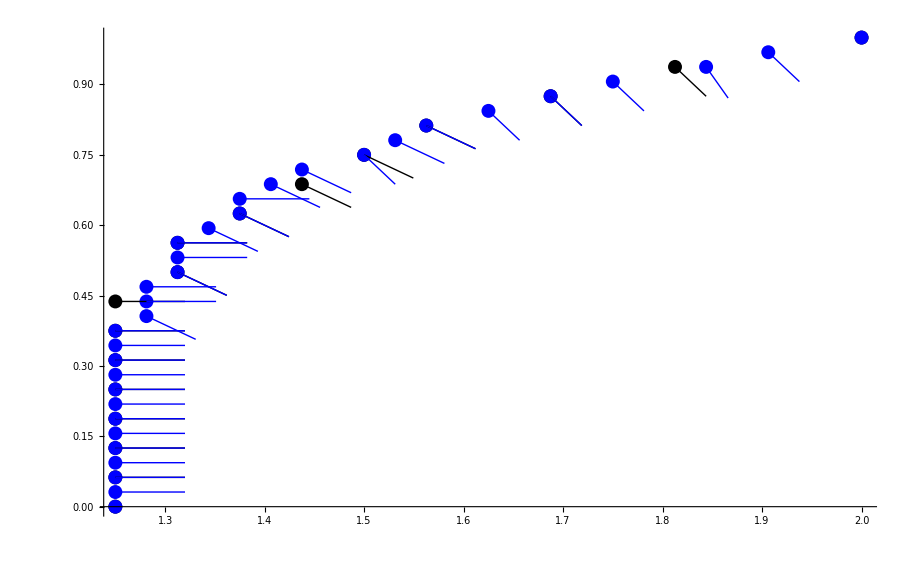

```mathematica
ListPlot[{a1,a2},PlotStyle->{Black,Blue}, Epilog->{Black,Arrowheads[0], b1, Blue,Arrowheads[0], b2}]
```

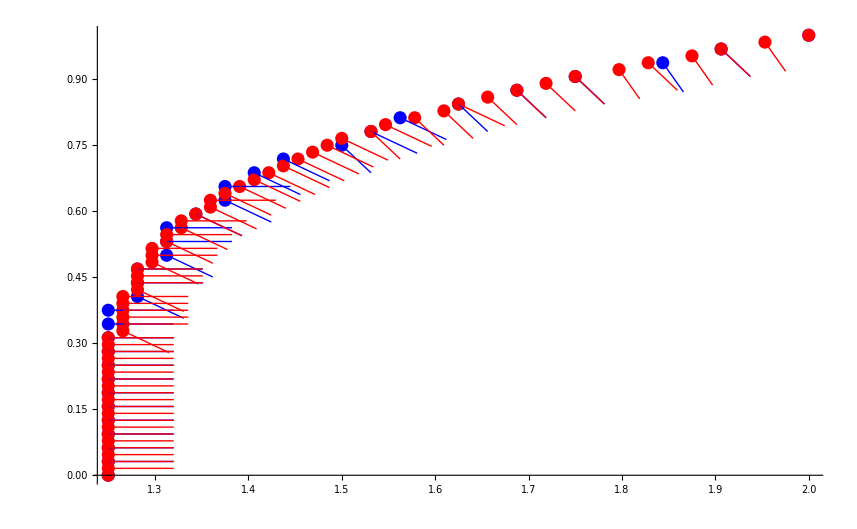

```mathematica
ListPlot[{a2,a3},PlotStyle->{Blue, Red}, Epilog->{ Blue,Arrowheads[0], b2, Red,Arrowheads[0], b3}]
```

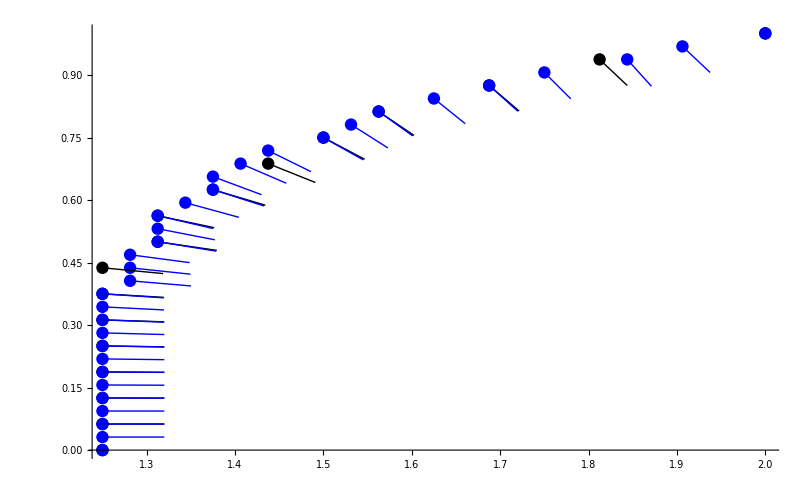

```mathematica
c1={Arrow[{{1.250000,0.062500},{1.320000,0.062487}}],Arrow[{{1.250000,0.125000},{1.320000,0.124808}}],Arrow[{{1.250000,0.187500},{1.319995,0.186667}}],Arrow[{{1.250000,0.250000},{1.319964,0.247758}}],Arrow[{{1.250000,0.312500},{1.319841,0.307781}}],Arrow[{{1.250000,0.375000},{1.319478,0.366464}}],Arrow[{{1.250000,0.437500},{1.318610,0.423618}}],Arrow[{{1.312500,0.500000},{1.379354,0.479251}}],Arrow[{{1.312500,0.562500},{1.376302,0.533703}}],Arrow[{{1.375000,0.625000},{1.434234,0.587700}}],Arrow[{{1.437500,0.687500},{1.490841,0.642171}}],Arrow[{{1.500000,0.750000},{1.546713,0.697867}}],Arrow[{{1.562500,0.812500},{1.602563,0.755098}}],Arrow[{{1.687500,0.875000},{1.721430,0.813773}}],Arrow[{{1.812500,0.937500},{1.843805,0.874890}}]};

c2={Arrow[{{1.250000,0.031250},{1.320000,0.031248}}],Arrow[{{1.250000,0.062500},{1.320000,0.062476}}],Arrow[{{1.250000,0.093750},{1.320000,0.093646}}],Arrow[{{1.250000,0.125000},{1.319999,0.124720}}],Arrow[{{1.250000,0.156250},{1.319998,0.155659}}],Arrow[{{1.250000,0.187500},{1.319992,0.186425}}],Arrow[{{1.250000,0.218750},{1.319978,0.216980}}],Arrow[{{1.250000,0.250000},{1.319947,0.247286}}],Arrow[{{1.250000,0.281250},{1.319889,0.277307}}],Arrow[{{1.250000,0.312500},{1.319784,0.307007}}],Arrow[{{1.250000,0.343750},{1.319608,0.336356}}],Arrow[{{1.250000,0.375000},{1.319329,0.365328}}],Arrow[{{1.281250,0.406250},{1.350154,0.393909}}],Arrow[{{1.281250,0.437500},{1.349534,0.422098}}],Arrow[{{1.281250,0.468750},{1.348667,0.449911}}],Arrow[{{1.312500,0.500000},{1.378748,0.477390}}],Arrow[{{1.312500,0.531250},{1.377230,0.504604}}],Arrow[{{1.312500,0.562500},{1.375333,0.531645}}],Arrow[{{1.343750,0.593750},{1.404300,0.558625}}],Arrow[{{1.375000,0.625000},{1.432904,0.585666}}],Arrow[{{1.375000,0.656250},{1.429949,0.612884}}],Arrow[{{1.406250,0.687500},{1.458013,0.640376}}],Arrow[{{1.437500,0.718750},{1.485936,0.668214}}],Arrow[{{1.500000,0.750000},{1.545063,0.696434}}],Arrow[{{1.531250,0.781250},{1.572977,0.725046}}],Arrow[{{1.562500,0.812500},{1.600997,0.754036}}],Arrow[{{1.625000,0.843750},{1.660424,0.783375}}],Arrow[{{1.687500,0.875000},{1.720040,0.813023}}],Arrow[{{1.750000,0.906250},{1.779863,0.842940}}],Arrow[{{1.843750,0.937500},{1.871148,0.873085}}],Arrow[{{1.906250,0.968750},{1.937555,0.906140}}]};
c3={Arrow[{{1.250000,0.015625},{1.320000,0.015625}}],Arrow[{{1.250000,0.031250},{1.320000,0.031247}}],Arrow[{{1.250000,0.046875},{1.320000,0.046862}}],Arrow[{{1.250000,0.062500},{1.320000,0.062465}}],Arrow[{{1.250000,0.078125},{1.320000,0.078051}}],Arrow[{{1.250000,0.093750},{1.320000,0.093616}}],Arrow[{{1.250000,0.109375},{1.320000,0.109154}}],Arrow[{{1.250000,0.125000},{1.319999,0.124661}}],Arrow[{{1.250000,0.140625},{1.319998,0.140131}}],Arrow[{{1.250000,0.156250},{1.319997,0.155561}}],Arrow[{{1.250000,0.171875},{1.319994,0.170946}}],Arrow[{{1.250000,0.187500},{1.319989,0.186280}}],Arrow[{{1.250000,0.203125},{1.319982,0.201558}}],Arrow[{{1.250000,0.218750},{1.319972,0.216777}}],Arrow[{{1.250000,0.234375},{1.319957,0.231931}}],Arrow[{{1.250000,0.250000},{1.319936,0.247016}}],Arrow[{{1.250000,0.265625},{1.319908,0.262028}}],Arrow[{{1.250000,0.281250},{1.319868,0.276961}}],Arrow[{{1.250000,0.296875},{1.319817,0.291812}}],Arrow[{{1.250000,0.312500},{1.319749,0.306577}}],Arrow[{{1.265625,0.328125},{1.335287,0.321253}}],Arrow[{{1.265625,0.343750},{1.335176,0.335835}}],Arrow[{{1.265625,0.359375},{1.335037,0.350322}}],Arrow[{{1.265625,0.375000},{1.334865,0.364712}}],Arrow[{{1.265625,0.390625},{1.334653,0.379003}}],Arrow[{{1.265625,0.406250},{1.334397,0.393195}}],Arrow[{{1.281250,0.421875},{1.349714,0.407289}}],Arrow[{{1.281250,0.437500},{1.349347,0.421288}}],Arrow[{{1.281250,0.453125},{1.348914,0.435194}}],Arrow[{{1.281250,0.468750},{1.348410,0.449013}}],Arrow[{{1.296875,0.484375},{1.363452,0.462752}}],Arrow[{{1.296875,0.500000},{1.362784,0.476419}}],Arrow[{{1.296875,0.515625},{1.362026,0.490024}}],Arrow[{{1.312500,0.531250},{1.376799,0.503580}}],Arrow[{{1.312500,0.546875},{1.375851,0.517098}}],Arrow[{{1.328125,0.562500},{1.390431,0.530594}}],Arrow[{{1.328125,0.578125},{1.389289,0.544081}}],Arrow[{{1.343750,0.593750},{1.403679,0.557577}}],Arrow[{{1.359375,0.609375},{1.417981,0.571095}}],Arrow[{{1.359375,0.625000},{1.416575,0.584650}}],Arrow[{{1.375000,0.640625},{1.430722,0.598257}}],Arrow[{{1.390625,0.656250},{1.444805,0.611927}}],Arrow[{{1.406250,0.671875},{1.458836,0.625672}}],Arrow[{{1.421875,0.687500},{1.472825,0.639499}}],Arrow[{{1.437500,0.703125},{1.486785,0.653416}}],Arrow[{{1.453125,0.718750},{1.500728,0.667428}}],Arrow[{{1.468750,0.734375},{1.514665,0.681537}}],Arrow[{{1.484375,0.750000},{1.528606,0.695745}}],Arrow[{{1.500000,0.765625},{1.542562,0.710051}}],Arrow[{{1.531250,0.781250},{1.572165,0.724453}}],Arrow[{{1.546875,0.796875},{1.586174,0.738948}}],Arrow[{{1.578125,0.812500},{1.615845,0.753532}}],Arrow[{{1.609375,0.828125},{1.645558,0.768201}}],Arrow[{{1.625000,0.843750},{1.659691,0.782951}}],Arrow[{{1.656250,0.859375},{1.689498,0.797775}}],Arrow[{{1.687500,0.875000},{1.719357,0.812669}}],Arrow[{{1.718750,0.890625},{1.749268,0.827628}}],Arrow[{{1.750000,0.906250},{1.779233,0.842646}}],Arrow[{{1.796875,0.921875},{1.824875,0.857719}}],Arrow[{{1.828125,0.937500},{1.854945,0.872842}}],Arrow[{{1.875000,0.953125},{1.900692,0.888010}}],Arrow[{{1.906250,0.968750},{1.930865,0.903221}}],Arrow[{{1.953125,0.984375},{1.975261,0.917967}}]};
ListPlot[{a1,a2},PlotStyle->{Black,Blue}, Epilog->{Black,Arrowheads[0], c1, Blue,Arrowheads[0], c2}]
```

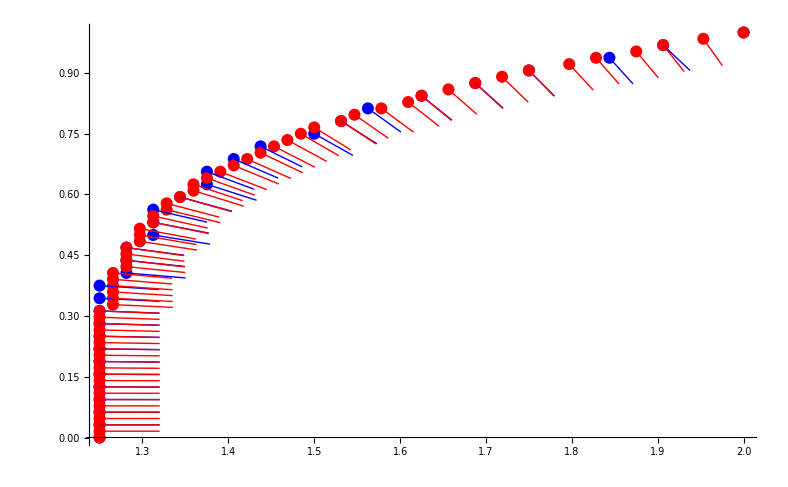

```mathematica
ListPlot[{a2,a3},PlotStyle->{Blue, Red}, Epilog->{ Blue,Arrowheads[0], c2, Red,Arrowheads[0], c3}]
```

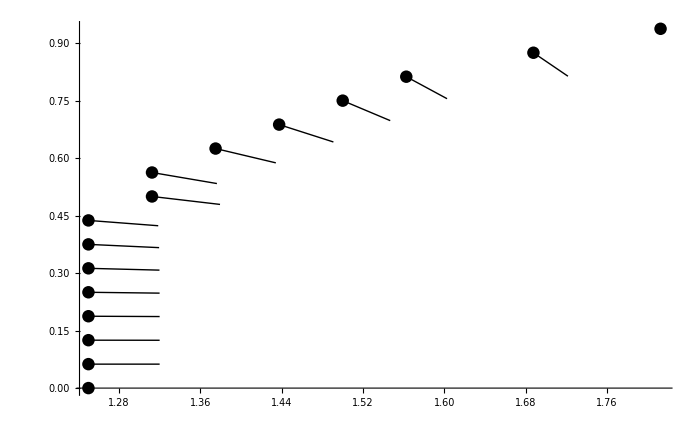

```mathematica
boundary1={{1.250000,0.000000},{1.250000,0.062500},{1.250000,0.125000},{1.250000,0.187500},{1.250000,0.250000},{1.250000,0.312500},{1.250000,0.375000},{1.250000,0.437500},{1.312500,0.500000},{1.312500,0.562500},{1.375000,0.625000},{1.437500,0.687500},{1.500000,0.750000},{1.562500,0.812500},{1.687500,0.875000},{1.812500,0.937500}};
arrow1={
Arrow[{{1.250000,0.062500},{1.320000,0.062487}}],Arrow[{{1.250000,0.125000},{1.320000,0.124808}}],Arrow[{{1.250000,0.187500},{1.319995,0.186667}}],Arrow[{{1.250000,0.250000},{1.319964,0.247758}}],Arrow[{{1.250000,0.312500},{1.319841,0.307781}}],Arrow[{{1.250000,0.375000},{1.319478,0.366464}}],Arrow[{{1.250000,0.437500},{1.318610,0.423618}}],Arrow[{{1.312500,0.500000},{1.379354,0.479251}}],Arrow[{{1.312500,0.562500},{1.376302,0.533703}}],Arrow[{{1.375000,0.625000},{1.434234,0.587700}}],Arrow[{{1.437500,0.687500},{1.490841,0.642171}}],Arrow[{{1.500000,0.750000},{1.546713,0.697867}}],Arrow[{{1.562500,0.812500},{1.602563,0.755098}}],Arrow[{{1.687500,0.875000},{1.721430,0.813773}}]};
A1=ListPlot[boundary1,PlotStyle->{Black}, Epilog->{Black,Arrowheads[0], arrow1}]
```

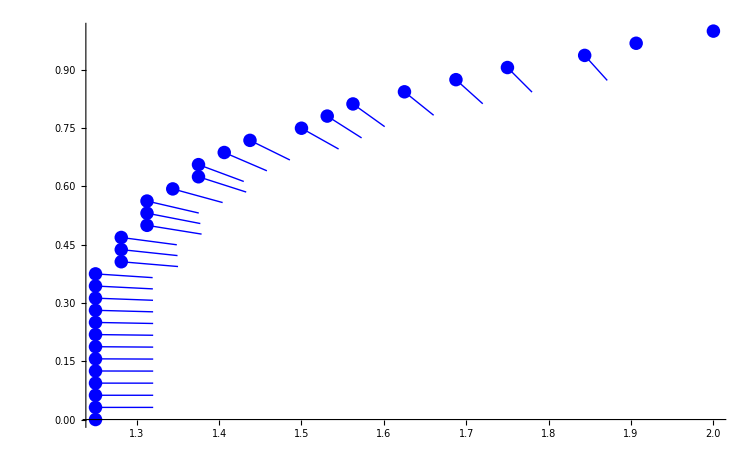

```mathematica
boundary2={{1.250000,0.000000},{1.250000,0.031250},{1.250000,0.062500},{1.250000,0.093750},{1.250000,0.125000},{1.250000,0.156250},{1.250000,0.187500},{1.250000,0.218750},{1.250000,0.250000},{1.250000,0.281250},{1.250000,0.312500},{1.250000,0.343750},{1.250000,0.375000},{1.281250,0.406250},{1.281250,0.437500},{1.281250,0.468750},{1.312500,0.500000},{1.312500,0.531250},{1.312500,0.562500},{1.343750,0.593750},{1.375000,0.625000},{1.375000,0.656250},{1.406250,0.687500},{1.437500,0.718750},{1.500000,0.750000},{1.531250,0.781250},{1.562500,0.812500},{1.625000,0.843750},{1.687500,0.875000},{1.750000,0.906250},{1.843750,0.937500},{1.906250,0.968750},{2.000000,1.000000}};
arrow2={Arrow[{{1.250000,0.031250},{1.320000,0.031248}}],Arrow[{{1.250000,0.062500},{1.320000,0.062476}}],Arrow[{{1.250000,0.093750},{1.320000,0.093646}}],Arrow[{{1.250000,0.125000},{1.319999,0.124720}}],Arrow[{{1.250000,0.156250},{1.319998,0.155659}}],Arrow[{{1.250000,0.187500},{1.319992,0.186425}}],Arrow[{{1.250000,0.218750},{1.319978,0.216980}}],Arrow[{{1.250000,0.250000},{1.319947,0.247286}}],Arrow[{{1.250000,0.281250},{1.319889,0.277307}}],Arrow[{{1.250000,0.312500},{1.319784,0.307007}}],Arrow[{{1.250000,0.343750},{1.319608,0.336356}}],Arrow[{{1.250000,0.375000},{1.319329,0.365328}}],Arrow[{{1.281250,0.406250},{1.350154,0.393909}}],Arrow[{{1.281250,0.437500},{1.349534,0.422098}}],Arrow[{{1.281250,0.468750},{1.348667,0.449911}}],Arrow[{{1.312500,0.500000},{1.378748,0.477390}}],Arrow[{{1.312500,0.531250},{1.377230,0.504604}}],Arrow[{{1.312500,0.562500},{1.375333,0.531645}}],Arrow[{{1.343750,0.593750},{1.404300,0.558625}}],Arrow[{{1.375000,0.625000},{1.432904,0.585666}}],Arrow[{{1.375000,0.656250},{1.429949,0.612884}}],Arrow[{{1.406250,0.687500},{1.458013,0.640376}}],Arrow[{{1.437500,0.718750},{1.485936,0.668214}}],Arrow[{{1.500000,0.750000},{1.545063,0.696434}}],Arrow[{{1.531250,0.781250},{1.572977,0.725046}}],Arrow[{{1.562500,0.812500},{1.600997,0.754036}}],Arrow[{{1.625000,0.843750},{1.660424,0.783375}}],Arrow[{{1.687500,0.875000},{1.720040,0.813023}}],Arrow[{{1.750000,0.906250},{1.779863,0.842940}}],Arrow[{{1.843750,0.937500},{1.871148,0.873085}}]};
A2=ListPlot[boundary2,PlotStyle->{Blue}, Epilog->{Blue,Arrowheads[0], arrow2}]
```

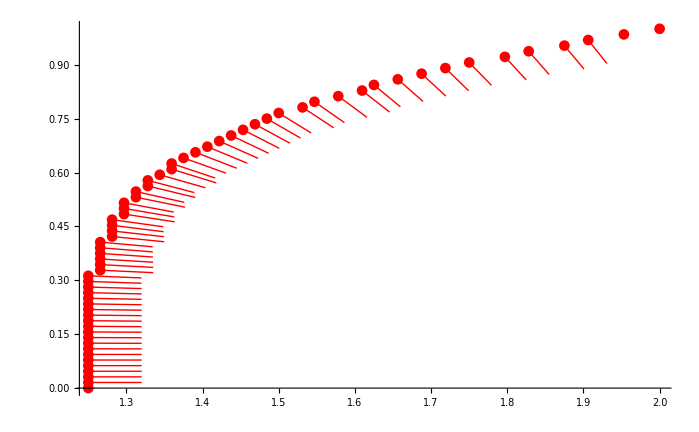

```mathematica
boundary3={
{1.250000,0.000000},{1.250000,0.015625},{1.250000,0.031250},{1.250000,0.046875},{1.250000,0.062500},{1.250000,0.078125},{1.250000,0.093750},{1.250000,0.109375},{1.250000,0.125000},{1.250000,0.140625},{1.250000,0.156250},{1.250000,0.171875},{1.250000,0.187500},{1.250000,0.203125},{1.250000,0.218750},{1.250000,0.234375},{1.250000,0.250000},{1.250000,0.265625},{1.250000,0.281250},{1.250000,0.296875},{1.250000,0.312500},{1.265625,0.328125},{1.265625,0.343750},{1.265625,0.359375},{1.265625,0.375000},{1.265625,0.390625},{1.265625,0.406250},{1.281250,0.421875},{1.281250,0.437500},{1.281250,0.453125},{1.281250,0.468750},{1.296875,0.484375},{1.296875,0.500000},{1.296875,0.515625},{1.312500,0.531250},{1.312500,0.546875},{1.328125,0.562500},{1.328125,0.578125},{1.343750,0.593750},{1.359375,0.609375},{1.359375,0.625000},{1.375000,0.640625},{1.390625,0.656250},{1.406250,0.671875},{1.421875,0.687500},{1.437500,0.703125},{1.453125,0.718750},{1.468750,0.734375},{1.484375,0.750000},{1.500000,0.765625},{1.531250,0.781250},{1.546875,0.796875},{1.578125,0.812500},{1.609375,0.828125},{1.625000,0.843750},{1.656250,0.859375},{1.687500,0.875000},{1.718750,0.890625},{1.750000,0.906250},{1.796875,0.921875},{1.828125,0.937500},{1.875000,0.953125},{1.906250,0.968750},{1.953125,0.984375},{2.000000,1.000000}};

arrow3={Arrow[{{1.250000,0.015625},{1.320000,0.015625}}],Arrow[{{1.250000,0.031250},{1.320000,0.031247}}],Arrow[{{1.250000,0.046875},{1.320000,0.046862}}],Arrow[{{1.250000,0.062500},{1.320000,0.062465}}],Arrow[{{1.250000,0.078125},{1.320000,0.078051}}],Arrow[{{1.250000,0.093750},{1.320000,0.093616}}],Arrow[{{1.250000,0.109375},{1.320000,0.109154}}],Arrow[{{1.250000,0.125000},{1.319999,0.124661}}],Arrow[{{1.250000,0.140625},{1.319998,0.140131}}],Arrow[{{1.250000,0.156250},{1.319997,0.155561}}],Arrow[{{1.250000,0.171875},{1.319994,0.170946}}],Arrow[{{1.250000,0.187500},{1.319989,0.186280}}],Arrow[{{1.250000,0.203125},{1.319982,0.201558}}],Arrow[{{1.250000,0.218750},{1.319972,0.216777}}],Arrow[{{1.250000,0.234375},{1.319957,0.231931}}],Arrow[{{1.250000,0.250000},{1.319936,0.247016}}],Arrow[{{1.250000,0.265625},{1.319908,0.262028}}],Arrow[{{1.250000,0.281250},{1.319868,0.276961}}],Arrow[{{1.250000,0.296875},{1.319817,0.291812}}],Arrow[{{1.250000,0.312500},{1.319749,0.306577}}],Arrow[{{1.265625,0.328125},{1.335287,0.321253}}],Arrow[{{1.265625,0.343750},{1.335176,0.335835}}],Arrow[{{1.265625,0.359375},{1.335037,0.350322}}],Arrow[{{1.265625,0.375000},{1.334865,0.364712}}],Arrow[{{1.265625,0.390625},{1.334653,0.379003}}],Arrow[{{1.265625,0.406250},{1.334397,0.393195}}],Arrow[{{1.281250,0.421875},{1.349714,0.407289}}],Arrow[{{1.281250,0.437500},{1.349347,0.421288}}],Arrow[{{1.281250,0.453125},{1.348914,0.435194}}],Arrow[{{1.281250,0.468750},{1.348410,0.449013}}],Arrow[{{1.296875,0.484375},{1.363452,0.462752}}],Arrow[{{1.296875,0.500000},{1.362784,0.476419}}],Arrow[{{1.296875,0.515625},{1.362026,0.490024}}],Arrow[{{1.312500,0.531250},{1.376799,0.503580}}],Arrow[{{1.312500,0.546875},{1.375851,0.517098}}],Arrow[{{1.328125,0.562500},{1.390431,0.530594}}],Arrow[{{1.328125,0.578125},{1.389289,0.544081}}],Arrow[{{1.343750,0.593750},{1.403679,0.557577}}],Arrow[{{1.359375,0.609375},{1.417981,0.571095}}],Arrow[{{1.359375,0.625000},{1.416575,0.584650}}],Arrow[{{1.375000,0.640625},{1.430722,0.598257}}],Arrow[{{1.390625,0.656250},{1.444805,0.611927}}],Arrow[{{1.406250,0.671875},{1.458836,0.625672}}],Arrow[{{1.421875,0.687500},{1.472825,0.639499}}],Arrow[{{1.437500,0.703125},{1.486785,0.653416}}],Arrow[{{1.453125,0.718750},{1.500728,0.667428}}],Arrow[{{1.468750,0.734375},{1.514665,0.681537}}],Arrow[{{1.484375,0.750000},{1.528606,0.695745}}],Arrow[{{1.500000,0.765625},{1.542562,0.710051}}],Arrow[{{1.531250,0.781250},{1.572165,0.724453}}],Arrow[{{1.546875,0.796875},{1.586174,0.738948}}],Arrow[{{1.578125,0.812500},{1.615845,0.753532}}],Arrow[{{1.609375,0.828125},{1.645558,0.768201}}],Arrow[{{1.625000,0.843750},{1.659691,0.782951}}],Arrow[{{1.656250,0.859375},{1.689498,0.797775}}],Arrow[{{1.687500,0.875000},{1.719357,0.812669}}],Arrow[{{1.718750,0.890625},{1.749268,0.827628}}],Arrow[{{1.750000,0.906250},{1.779233,0.842646}}],Arrow[{{1.796875,0.921875},{1.824875,0.857719}}],Arrow[{{1.828125,0.937500},{1.854945,0.872842}}],Arrow[{{1.875000,0.953125},{1.900692,0.888010}}],Arrow[{{1.906250,0.968750},{1.930865,0.903221}}]};
A3=ListPlot[boundary3,PlotStyle->{Red}, Epilog->{Red,Arrowheads[0], arrow3}]
```

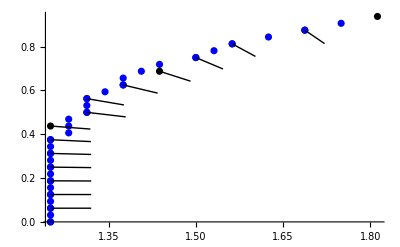

```mathematica
Show[A1,A2]
```

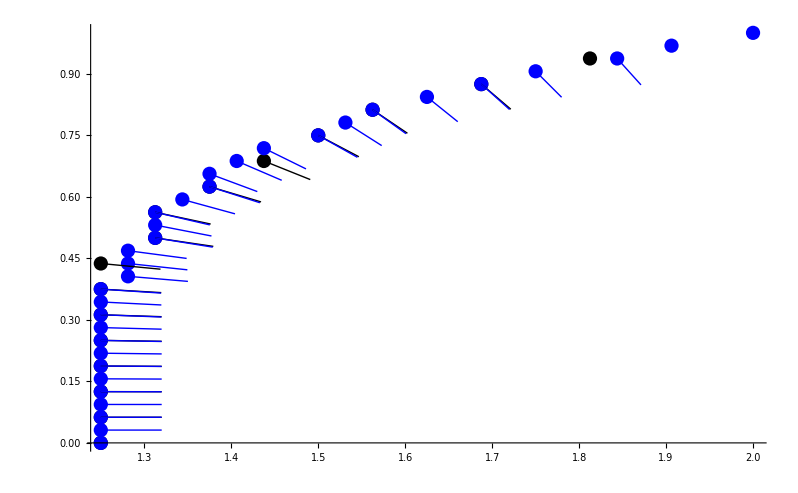

```mathematica
ListPlot[{boundary1,boundary2},PlotStyle->{Black,Blue}, Epilog->{Black,Arrowheads[0], arrow1, Blue,Arrowheads[0], arrow2}]
```

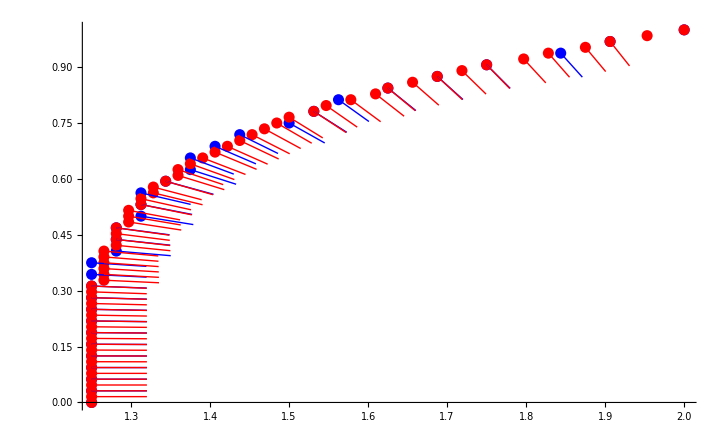

```mathematica
ListPlot[{boundary2,boundary3},PlotStyle->{Blue,Red}, Epilog->{Blue,Arrowheads[0], arrow2, Red,Arrowheads[0], arrow3}]
```

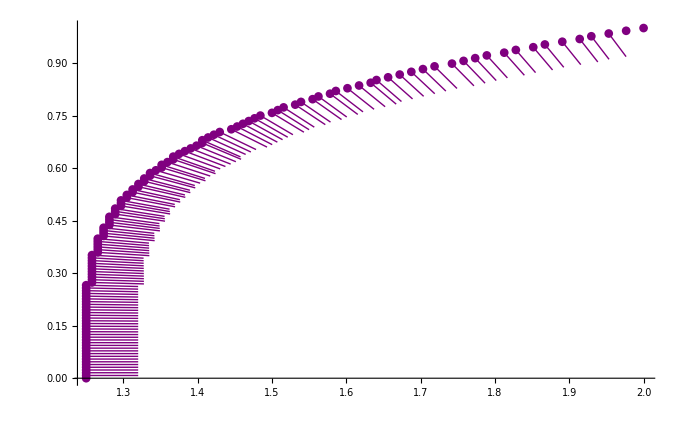

```mathematica
boundary4={{1.250000,0.000000},{1.250000,0.007812},{1.250000,0.015625},{1.250000,0.023438},{1.250000,0.031250},{1.250000,0.039062},{1.250000,0.046875},{1.250000,0.054688},{1.250000,0.062500},{1.250000,0.070312},{1.250000,0.078125},{1.250000,0.085938},{1.250000,0.093750},{1.250000,0.101562},{1.250000,0.109375},{1.250000,0.117188},{1.250000,0.125000},{1.250000,0.132812},{1.250000,0.140625},{1.250000,0.148438},{1.250000,0.156250},{1.250000,0.164062},{1.250000,0.171875},{1.250000,0.179688},{1.250000,0.187500},{1.250000,0.195312},{1.250000,0.203125},{1.250000,0.210938},{1.250000,0.218750},{1.250000,0.226562},{1.250000,0.234375},{1.250000,0.242188},{1.250000,0.250000},{1.250000,0.257812},{1.250000,0.265625},{1.257812,0.273438},{1.257812,0.281250},{1.257812,0.289062},{1.257812,0.296875},{1.257812,0.304688},{1.257812,0.312500},{1.257812,0.320312},{1.257812,0.328125},{1.257812,0.335938},{1.257812,0.343750},{1.257812,0.351562},{1.265625,0.359375},{1.265625,0.367188},{1.265625,0.375000},{1.265625,0.382812},{1.265625,0.390625},{1.265625,0.398438},{1.273438,0.406250},{1.273438,0.414062},{1.273438,0.421875},{1.273438,0.429688},{1.281250,0.437500},{1.281250,0.445312},{1.281250,0.453125},{1.281250,0.460938},{1.289062,0.468750},{1.289062,0.476562},{1.289062,0.484375},{1.296875,0.492188},{1.296875,0.500000},{1.296875,0.507812},{1.304688,0.515625},{1.304688,0.523438},{1.312500,0.531250},{1.312500,0.539062},{1.320312,0.546875},{1.320312,0.554688},{1.328125,0.562500},{1.328125,0.570312},{1.335938,0.578125},{1.335938,0.585938},{1.343750,0.593750},{1.351562,0.601562},{1.351562,0.609375},{1.359375,0.617188},{1.367188,0.625000},{1.367188,0.632812},{1.375000,0.640625},{1.382812,0.648438},{1.390625,0.656250},{1.398438,0.664062},{1.406250,0.671875},{1.406250,0.679688},{1.414062,0.687500},{1.421875,0.695312},{1.429688,0.703125},{1.445312,0.710938},{1.453125,0.718750},{1.460938,0.726562},{1.468750,0.734375},{1.476562,0.742188},{1.484375,0.750000},{1.500000,0.757812},{1.507812,0.765625},{1.515625,0.773438},{1.531250,0.781250},{1.539062,0.789062},{1.554688,0.796875},{1.562500,0.804688},{1.578125,0.812500},{1.585938,0.820312},{1.601562,0.828125},{1.617188,0.835938},{1.632812,0.843750},{1.640625,0.851562},{1.656250,0.859375},{1.671875,0.867188},{1.687500,0.875000},{1.703125,0.882812},{1.718750,0.890625},{1.742188,0.898438},{1.757812,0.906250},{1.773438,0.914062},{1.789062,0.921875},{1.812500,0.929688},{1.828125,0.937500},{1.851562,0.945312},{1.867188,0.953125},{1.890625,0.960938},{1.914062,0.968750},{1.929688,0.976562},{1.953125,0.984375},{1.976562,0.992188},{2.000000,1.000000}};
arrow4={Arrow[{{1.250000,0.007812},{1.320000,0.007812}}],Arrow[{{1.250000,0.015625},{1.320000,0.015625}}],Arrow[{{1.250000,0.023438},{1.320000,0.023436}}],Arrow[{{1.250000,0.031250},{1.320000,0.031246}}],Arrow[{{1.250000,0.039062},{1.320000,0.039053}}],Arrow[{{1.250000,0.046875},{1.320000,0.046858}}],Arrow[{{1.250000,0.054688},{1.320000,0.054660}}],Arrow[{{1.250000,0.062500},{1.320000,0.062458}}],Arrow[{{1.250000,0.070312},{1.320000,0.070251}}],Arrow[{{1.250000,0.078125},{1.320000,0.078039}}],Arrow[{{1.250000,0.085938},{1.320000,0.085821}}],Arrow[{{1.250000,0.093750},{1.320000,0.093597}}],Arrow[{{1.250000,0.101562},{1.320000,0.101367}}],Arrow[{{1.250000,0.109375},{1.320000,0.109128}}],Arrow[{{1.250000,0.117188},{1.319999,0.116882}}],Arrow[{{1.250000,0.125000},{1.319999,0.124627}}],Arrow[{{1.250000,0.132812},{1.319999,0.132362}}],Arrow[{{1.250000,0.140625},{1.319998,0.140088}}],Arrow[{{1.250000,0.148438},{1.319997,0.147803}}],Arrow[{{1.250000,0.156250},{1.319996,0.155507}}],Arrow[{{1.250000,0.164062},{1.319995,0.163199}}],Arrow[{{1.250000,0.171875},{1.319993,0.170879}}],Arrow[{{1.250000,0.179688},{1.319991,0.178546}}],Arrow[{{1.250000,0.187500},{1.319988,0.186200}}],Arrow[{{1.250000,0.195312},{1.319985,0.193840}}],Arrow[{{1.250000,0.203125},{1.319980,0.201464}}],Arrow[{{1.250000,0.210938},{1.319975,0.209074}}],Arrow[{{1.250000,0.218750},{1.319969,0.216668}}],Arrow[{{1.250000,0.226562},{1.319962,0.224245}}],Arrow[{{1.250000,0.234375},{1.319953,0.231805}}],Arrow[{{1.250000,0.242188},{1.319942,0.239348}}],Arrow[{{1.250000,0.250000},{1.319930,0.246873}}],Arrow[{{1.250000,0.257812},{1.319916,0.254378}}],Arrow[{{1.250000,0.265625},{1.319899,0.261865}}],Arrow[{{1.257812,0.273438},{1.327692,0.269332}}],Arrow[{{1.257812,0.281250},{1.327670,0.276778}}],Arrow[{{1.257812,0.289062},{1.327644,0.284204}}],Arrow[{{1.257812,0.296875},{1.327614,0.291608}}],Arrow[{{1.257812,0.304688},{1.327580,0.298991}}],Arrow[{{1.257812,0.312500},{1.327542,0.306352}}],Arrow[{{1.257812,0.320312},{1.327498,0.313689}}],Arrow[{{1.257812,0.328125},{1.327449,0.321004}}],Arrow[{{1.257812,0.335938},{1.327394,0.328295}}],Arrow[{{1.257812,0.343750},{1.327332,0.335563}}],Arrow[{{1.257812,0.351562},{1.327263,0.342807}}],Arrow[{{1.265625,0.359375},{1.334998,0.350026}}],Arrow[{{1.265625,0.367188},{1.334912,0.357221}}],Arrow[{{1.265625,0.375000},{1.334816,0.364391}}],Arrow[{{1.265625,0.382812},{1.334711,0.371537}}],Arrow[{{1.265625,0.390625},{1.334594,0.378657}}],Arrow[{{1.265625,0.398438},{1.334466,0.385753}}],Arrow[{{1.273438,0.406250},{1.342138,0.392825}}],Arrow[{{1.273438,0.414062},{1.341984,0.399872}}],Arrow[{{1.273438,0.421875},{1.341816,0.406895}}],Arrow[{{1.273438,0.429688},{1.341633,0.413894}}],Arrow[{{1.281250,0.437500},{1.349246,0.420870}}],Arrow[{{1.281250,0.445312},{1.349030,0.427823}}],Arrow[{{1.281250,0.453125},{1.348796,0.434754}}],Arrow[{{1.281250,0.460938},{1.348544,0.441664}}],Arrow[{{1.289062,0.468750},{1.356085,0.448553}}],Arrow[{{1.289062,0.476562},{1.355794,0.455422}}],Arrow[{{1.289062,0.484375},{1.355482,0.462273}}],Arrow[{{1.296875,0.492188},{1.362960,0.469106}}],Arrow[{{1.296875,0.500000},{1.362604,0.475923}}],Arrow[{{1.296875,0.507812},{1.362225,0.482726}}],Arrow[{{1.304688,0.515625},{1.369636,0.489515}}],Arrow[{{1.304688,0.523438},{1.369210,0.496292}}],Arrow[{{1.312500,0.531250},{1.376573,0.503060}}],Arrow[{{1.312500,0.539062},{1.376099,0.509819}}],Arrow[{{1.320312,0.546875},{1.383413,0.516571}}],Arrow[{{1.320312,0.554688},{1.382890,0.523318}}],Arrow[{{1.328125,0.562500},{1.390156,0.530063}}],Arrow[{{1.328125,0.570312},{1.389585,0.536807}}],Arrow[{{1.335938,0.578125},{1.396803,0.543551}}],Arrow[{{1.335938,0.585938},{1.396186,0.550299}}],Arrow[{{1.343750,0.593750},{1.403358,0.557051}}],Arrow[{{1.351562,0.601562},{1.410509,0.563809}}],Arrow[{{1.351562,0.609375},{1.409826,0.570577}}],Arrow[{{1.359375,0.617188},{1.416936,0.577354}}],Arrow[{{1.367188,0.625000},{1.424027,0.584143}}],Arrow[{{1.367188,0.632812},{1.423288,0.590947}}],Arrow[{{1.375000,0.640625},{1.430344,0.597765}}],Arrow[{{1.382812,0.648438},{1.437386,0.604600}}],Arrow[{{1.390625,0.656250},{1.444413,0.611452}}],Arrow[{{1.398438,0.664062},{1.451428,0.618324}}],Arrow[{{1.406250,0.671875},{1.458432,0.625217}}],Arrow[{{1.406250,0.679688},{1.457614,0.632130}}],Arrow[{{1.414062,0.687500},{1.464601,0.639066}}],Arrow[{{1.421875,0.695312},{1.471581,0.646024}}],Arrow[{{1.429688,0.703125},{1.478556,0.653006}}],Arrow[{{1.445312,0.710938},{1.493339,0.660012}}],Arrow[{{1.453125,0.718750},{1.500308,0.667042}}],Arrow[{{1.460938,0.726562},{1.507277,0.674097}}],Arrow[{{1.468750,0.734375},{1.514245,0.681176}}],Arrow[{{1.476562,0.742188},{1.521216,0.688279}}],Arrow[{{1.484375,0.750000},{1.528189,0.695408}}],Arrow[{{1.500000,0.757812},{1.542980,0.702561}}],Arrow[{{1.507812,0.765625},{1.549962,0.709738}}],Arrow[{{1.515625,0.773438},{1.556951,0.716939}}],Arrow[{{1.531250,0.781250},{1.571760,0.724163}}],Arrow[{{1.539062,0.789062},{1.578765,0.731411}}],Arrow[{{1.554688,0.796875},{1.593590,0.738681}}],Arrow[{{1.562500,0.804688},{1.600613,0.745973}}],Arrow[{{1.578125,0.812500},{1.615458,0.753287}}],Arrow[{{1.585938,0.820312},{1.622502,0.760621}}],Arrow[{{1.601562,0.828125},{1.637369,0.767976}}],Arrow[{{1.617188,0.835938},{1.652249,0.775351}}],Arrow[{{1.632812,0.843750},{1.667140,0.782745}}],Arrow[{{1.640625,0.851562},{1.674231,0.790157}}],Arrow[{{1.656250,0.859375},{1.689147,0.797587}}],Arrow[{{1.671875,0.867188},{1.704077,0.805034}}],Arrow[{{1.687500,0.875000},{1.719019,0.812498}}],Arrow[{{1.703125,0.882812},{1.733974,0.819977}}],Arrow[{{1.718750,0.890625},{1.748943,0.827471}}],Arrow[{{1.742188,0.898438},{1.771738,0.834981}}],Arrow[{{1.757812,0.906250},{1.786733,0.842504}}],Arrow[{{1.773438,0.914062},{1.801742,0.850040}}],Arrow[{{1.789062,0.921875},{1.816764,0.857589}}],Arrow[{{1.812500,0.929688},{1.839611,0.865151}}],Arrow[{{1.828125,0.937500},{1.854660,0.872724}}],Arrow[{{1.851562,0.945312},{1.877533,0.880308}}],Arrow[{{1.867188,0.953125},{1.892607,0.887903}}],Arrow[{{1.890625,0.960938},{1.915506,0.895509}}],Arrow[{{1.914062,0.968750},{1.938417,0.903123}}],Arrow[{{1.929688,0.976562},{1.953528,0.910747}}],Arrow[{{1.953125,0.984375},{1.976464,0.918380}}]};
A4=ListPlot[boundary4,PlotStyle->{Purple}, Epilog->{Purple,Arrowheads[0], arrow4}]
```

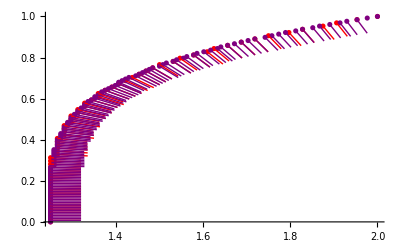

```mathematica
ListPlot[{boundary3,boundary4},PlotStyle->{Red, Purple}, Epilog->{Red,Arrowheads[0], arrow3, Purple,Arrowheads[0], arrow4}]
```

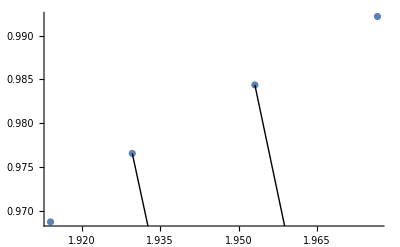

```mathematica
a={{1.914062,0.968750},{1.929688,0.976562},{1.953125,0.984375},{1.976562,0.992188}};
b={Arrow[{{1.929688,0.976562},{1.953528,0.910747}}],Arrow[{{1.953125,0.984375},{1.976464,0.918380}}]};
ListPlot[a, Epilog->{Arrowheads[0], b}]
```

```mathematica
{1.976562,0.992188}-{1.929688,0.976562}
```

{0.046874,0.015626}

```mathematica
{1.976464,0.918380}-{1.953125,0.984375}
```

{0.023339,-0.065995}

```mathematica
{0.04687399999999986,0.015625999999999918}.{0.023339,-0.06599500000000003}
```

0.0000627544

```mathematica
{{1.953125,0.984375}-{1.914062,0.968750}}.{{1.953528,0.910747}-{1.929688,0.976562}}
```

Dot::dotsh: Tensors {{0.039063,0.015625}} and {{0.02384,-0.065815}} have incompatible shapes.

{{0.039063,0.015625}}.{{0.02384,-0.065815}}

```mathematica
{1.953125,0.984375}-{1.914062,0.968750}
```

{0.039063,0.015625}

```mathematica
{1.953528,0.910747}-{1.929688,0.976562}
```

{0.02384,-0.065815}

```mathematica
{0.03906300000000007,0.015625}.{0.02383999999999986,-0.06581500000000007}
```

-0.0000970975

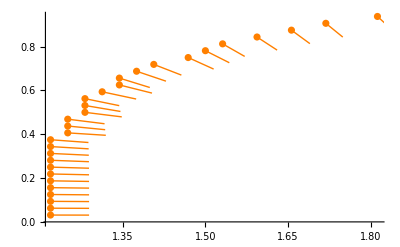

```mathematica
boundary22={{1.218750,0.031250},{1.218750,0.062500},{1.218750,0.093750},{1.218750,0.125000},{1.218750,0.156250},{1.218750,0.187500},{1.218750,0.218750},{1.218750,0.250000},{1.218750,0.281250},{1.218750,0.312500},{1.218750,0.343750},{1.218750,0.375000},{1.250000,0.406250},{1.250000,0.437500},{1.250000,0.468750},{1.281250,0.500000},{1.281250,0.531250},{1.281250,0.562500},{1.312500,0.593750},{1.343750,0.625000},{1.343750,0.656250},{1.375000,0.687500},{1.406250,0.718750},{1.468750,0.750000},{1.500000,0.781250},{1.531250,0.812500},{1.593750,0.843750},{1.656250,0.875000},{1.718750,0.906250},{1.812500,0.937500}};
arrow22={Arrow[{{1.218750,0.031250},{1.288749,0.030943}}],Arrow[{{1.218750,0.062500},{1.288747,0.061859}}],Arrow[{{1.218750,0.093750},{1.288742,0.092718}}],Arrow[{{1.218750,0.125000},{1.288734,0.123485}}],Arrow[{{1.218750,0.156250},{1.288718,0.154124}}],Arrow[{{1.218750,0.187500},{1.288690,0.184602}}],Arrow[{{1.218750,0.218750},{1.288643,0.214883}}],Arrow[{{1.218750,0.250000},{1.288567,0.244935}}],Arrow[{{1.218750,0.281250},{1.288445,0.274726}}],Arrow[{{1.218750,0.312500},{1.288259,0.304227}}],Arrow[{{1.218750,0.343750},{1.287983,0.333417}}],Arrow[{{1.218750,0.375000},{1.287588,0.362296}}],Arrow[{{1.250000,0.406250},{1.319129,0.395242}}],Arrow[{{1.250000,0.437500},{1.317961,0.420728}}],Arrow[{{1.250000,0.468750},{1.316813,0.447870}}],Arrow[{{1.281250,0.500000},{1.348109,0.479267}}],Arrow[{{1.281250,0.531250},{1.345715,0.503969}}],Arrow[{{1.281250,0.562500},{1.343512,0.530508}}],Arrow[{{1.312500,0.593750},{1.374228,0.560740}}],Arrow[{{1.343750,0.625000},{1.403014,0.587747}}],Arrow[{{1.343750,0.656250},{1.399023,0.613298}}],Arrow[{{1.375000,0.687500},{1.428389,0.642227}}],Arrow[{{1.406250,0.718750},{1.456379,0.669892}}],Arrow[{{1.468750,0.750000},{1.514959,0.697419}}],Arrow[{{1.500000,0.781250},{1.543415,0.726340}}],Arrow[{{1.531250,0.812500},{1.571378,0.755144}}],Arrow[{{1.593750,0.843750},{1.630209,0.783994}}],Arrow[{{1.656250,0.875000},{1.689760,0.813542}}],Arrow[{{1.718750,0.906250},{1.749512,0.843371}}],Arrow[{{1.812500,0.937500},{1.840519,0.873352}}]};
A22=ListPlot[boundary22,PlotStyle->{Orange}, Epilog->{Orange,Arrowheads[0], arrow22}]
```

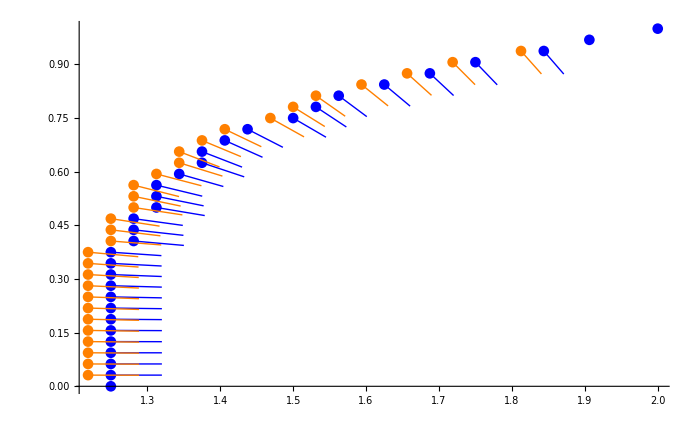

```mathematica
ListPlot[{boundary2,boundary22},PlotStyle->{Blue, Orange}, Epilog->{Blue,Arrowheads[0], arrow2,Orange,Arrowheads[0], arrow22}]
```

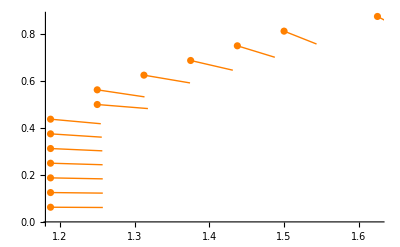

```mathematica
boundary11={{1.187500,0.062500},{1.187500,0.125000},{1.187500,0.187500},{1.187500,0.250000},{1.187500,0.312500},{1.187500,0.375000},{1.187500,0.437500},{1.250000,0.500000},{1.250000,0.562500},{1.312500,0.625000},{1.375000,0.687500},{1.437500,0.750000},{1.500000,0.812500},{1.625000,0.875000}};
arrow11={Arrow[{{1.187500,0.062500},{1.257491,0.061359}}],Arrow[{{1.187500,0.125000},{1.257457,0.122533}}],Arrow[{{1.187500,0.187500},{1.257373,0.183292}}],Arrow[{{1.187500,0.250000},{1.257188,0.243402}}],Arrow[{{1.187500,0.312500},{1.256803,0.302648}}],Arrow[{{1.187500,0.375000},{1.256061,0.360880}}],Arrow[{{1.187500,0.437500},{1.254757,0.418097}}],Arrow[{{1.250000,0.500000},{1.317819,0.482662}}],Arrow[{{1.250000,0.562500},{1.313259,0.532529}}],Arrow[{{1.312500,0.625000},{1.374165,0.591873}}],Arrow[{{1.375000,0.687500},{1.431431,0.646081}}],Arrow[{{1.437500,0.750000},{1.487643,0.701156}}],Arrow[{{1.500000,0.812500},{1.543468,0.757632}}],Arrow[{{1.625000,0.875000},{1.661018,0.814977}}]};
A11=ListPlot[boundary11,PlotStyle->{Orange}, Epilog->{Orange,Arrowheads[0], arrow11}]
```

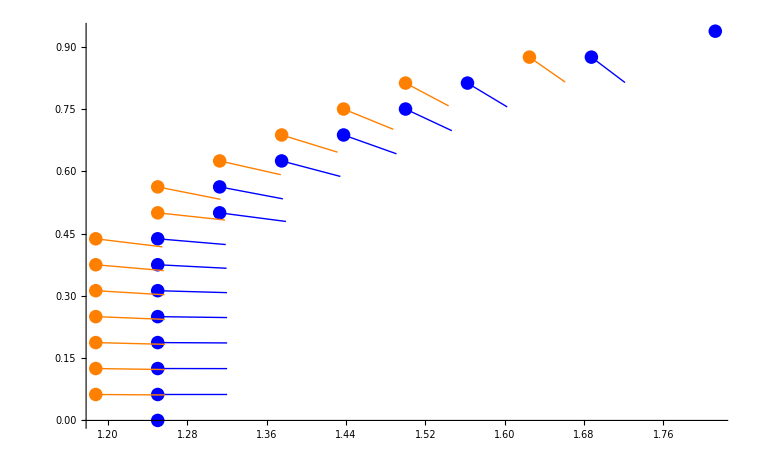

```mathematica
ListPlot[{boundary1,boundary11},PlotStyle->{Blue, Orange}, Epilog->{Blue,Arrowheads[0], arrow1,Orange,Arrowheads[0], arrow11}]
```

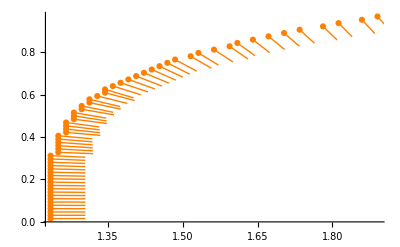

```mathematica
boundary33={{1.234375,0.015625},{1.234375,0.031250},{1.234375,0.046875},{1.234375,0.062500},{1.234375,0.078125},{1.234375,0.093750},{1.234375,0.109375},{1.234375,0.125000},{1.234375,0.140625},{1.234375,0.156250},{1.234375,0.171875},{1.234375,0.187500},{1.234375,0.203125},{1.234375,0.218750},{1.234375,0.234375},{1.234375,0.250000},{1.234375,0.265625},{1.234375,0.281250},{1.234375,0.296875},{1.234375,0.312500},{1.250000,0.328125},{1.250000,0.343750},{1.250000,0.359375},{1.250000,0.375000},{1.250000,0.390625},{1.250000,0.406250},{1.265625,0.421875},{1.265625,0.437500},{1.265625,0.453125},{1.265625,0.468750},{1.281250,0.484375},{1.281250,0.500000},{1.281250,0.515625},{1.296875,0.531250},{1.296875,0.546875},{1.312500,0.562500},{1.312500,0.578125},{1.328125,0.593750},{1.343750,0.609375},{1.343750,0.625000},{1.359375,0.640625},{1.375000,0.656250},{1.390625,0.671875},{1.406250,0.687500},{1.421875,0.703125},{1.437500,0.718750},{1.453125,0.734375},{1.468750,0.750000},{1.484375,0.765625},{1.515625,0.781250},{1.531250,0.796875},{1.562500,0.812500},{1.593750,0.828125},{1.609375,0.843750},{1.640625,0.859375},{1.671875,0.875000},{1.703125,0.890625},{1.734375,0.906250},{1.781250,0.921875},{1.812500,0.937500},{1.859375,0.953125},{1.890625,0.968750}};
arrow33=
{Arrow[{{1.234375,0.015625},{1.304375,0.015544}}],Arrow[{{1.234375,0.031250},{1.304375,0.031085}}],Arrow[{{1.234375,0.046875},{1.304375,0.046619}}],Arrow[{{1.234375,0.062500},{1.304374,0.062140}}],Arrow[{{1.234375,0.078125},{1.304373,0.077644}}],Arrow[{{1.234375,0.093750},{1.304372,0.093128}}],Arrow[{{1.234375,0.109375},{1.304371,0.108585}}],Arrow[{{1.234375,0.125000},{1.304368,0.124013}}],Arrow[{{1.234375,0.140625},{1.304364,0.139405}}],Arrow[{{1.234375,0.156250},{1.304359,0.154757}}],Arrow[{{1.234375,0.171875},{1.304352,0.170065}}],Arrow[{{1.234375,0.187500},{1.304341,0.185323}}],Arrow[{{1.234375,0.203125},{1.304327,0.200528}}],Arrow[{{1.234375,0.218750},{1.304307,0.215674}}],Arrow[{{1.234375,0.234375},{1.304281,0.230758}}],Arrow[{{1.234375,0.250000},{1.304247,0.245773}}],Arrow[{{1.234375,0.265625},{1.304203,0.260715}}],Arrow[{{1.234375,0.281250},{1.304145,0.275579}}],Arrow[{{1.234375,0.296875},{1.304071,0.290360}}],Arrow[{{1.234375,0.312500},{1.303978,0.305055}}],Arrow[{{1.250000,0.328125},{1.319707,0.321727}}],Arrow[{{1.250000,0.343750},{1.319457,0.335048}}],Arrow[{{1.250000,0.359375},{1.319245,0.349121}}],Arrow[{{1.250000,0.375000},{1.319022,0.363338}}],Arrow[{{1.250000,0.390625},{1.318766,0.377541}}],Arrow[{{1.250000,0.406250},{1.318470,0.391696}}],Arrow[{{1.265625,0.421875},{1.334247,0.408054}}],Arrow[{{1.265625,0.437500},{1.333563,0.420635}}],Arrow[{{1.265625,0.453125},{1.332995,0.434118}}],Arrow[{{1.265625,0.468750},{1.332424,0.447823}}],Arrow[{{1.281250,0.484375},{1.348125,0.463693}}],Arrow[{{1.281250,0.500000},{1.347008,0.476002}}],Arrow[{{1.281250,0.515625},{1.346092,0.489253}}],Arrow[{{1.296875,0.531250},{1.361608,0.504611}}],Arrow[{{1.296875,0.546875},{1.360154,0.516946}}],Arrow[{{1.312500,0.562500},{1.375337,0.531654}}],Arrow[{{1.312500,0.578125},{1.373674,0.544100}}],Arrow[{{1.328125,0.593750},{1.388681,0.558636}}],Arrow[{{1.343750,0.609375},{1.403027,0.572142}}],Arrow[{{1.343750,0.625000},{1.401112,0.584880}}],Arrow[{{1.359375,0.640625},{1.415845,0.599259}}],Arrow[{{1.375000,0.656250},{1.429960,0.612898}}],Arrow[{{1.390625,0.671875},{1.444016,0.626605}}],Arrow[{{1.406250,0.687500},{1.458026,0.640391}}],Arrow[{{1.421875,0.703125},{1.472000,0.654263}}],Arrow[{{1.437500,0.718750},{1.485951,0.668228}}],Arrow[{{1.453125,0.734375},{1.499890,0.682288}}],Arrow[{{1.468750,0.750000},{1.513829,0.696447}}],Arrow[{{1.484375,0.765625},{1.527777,0.710704}}],Arrow[{{1.515625,0.781250},{1.557093,0.724855}}],Arrow[{{1.531250,0.796875},{1.571361,0.739507}}],Arrow[{{1.562500,0.812500},{1.600750,0.753874}}],Arrow[{{1.593750,0.828125},{1.630448,0.768516}}],Arrow[{{1.609375,0.843750},{1.644814,0.783384}}],Arrow[{{1.640625,0.859375},{1.674356,0.798038}}],Arrow[{{1.671875,0.875000},{1.704198,0.812909}}],Arrow[{{1.703125,0.890625},{1.734091,0.827847}}],Arrow[{{1.734375,0.906250},{1.764037,0.842845}}],Arrow[{{1.781250,0.921875},{1.809559,0.857855}}],Arrow[{{1.812500,0.937500},{1.839714,0.873007}}],Arrow[{{1.859375,0.953125},{1.885350,0.888123}}],Arrow[{{1.890625,0.968750},{1.915600,0.903357}}]};
A33=ListPlot[boundary33,PlotStyle->{Orange}, Epilog->{Orange,Arrowheads[0], arrow33}]
```

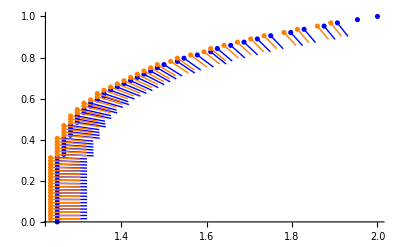

```mathematica
ListPlot[{boundary3,boundary33},PlotStyle->{Blue, Orange}, Epilog->{Blue,Arrowheads[0], arrow3,Orange,Arrowheads[0], arrow33}]
```

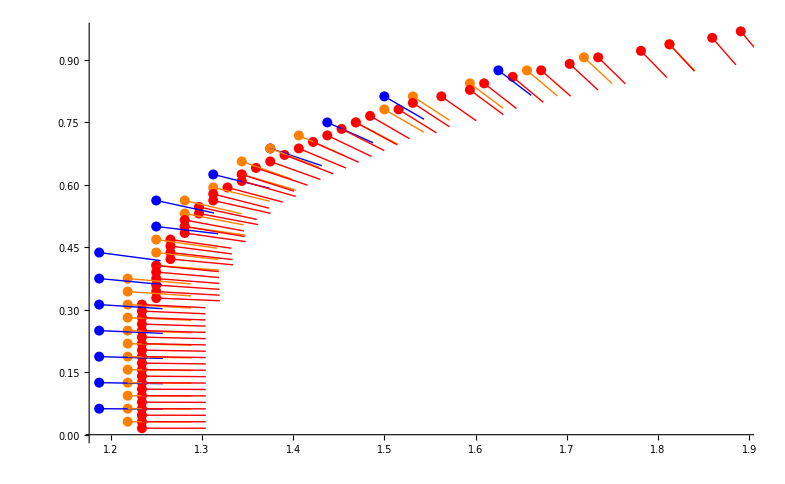

```mathematica
ListPlot[{boundary11,boundary22,boundary33},PlotStyle->{Blue, Orange,Red}, Epilog->{Blue,Arrowheads[0], arrow11,Orange,Arrowheads[0], arrow22, Red,Arrowheads[0], arrow33}]
```

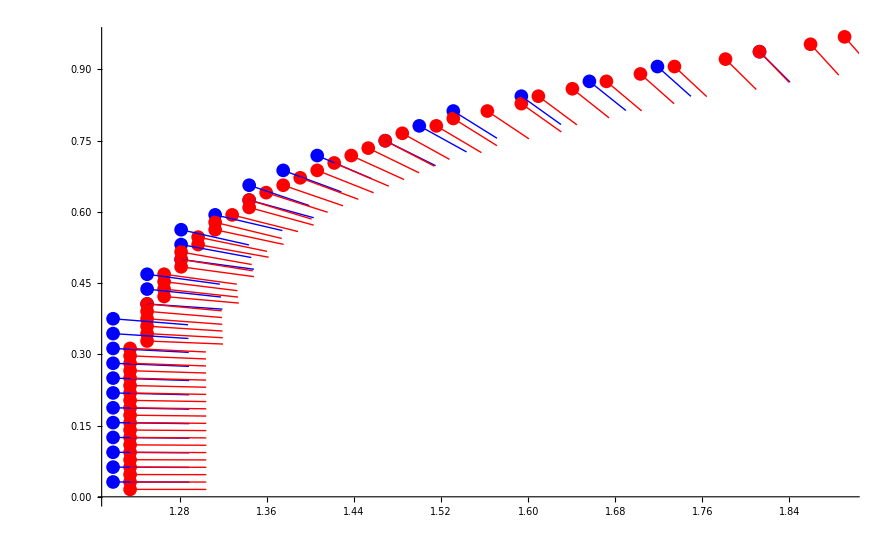

```mathematica
ListPlot[{boundary22,boundary33},PlotStyle->{Blue,Red}, Epilog->{Blue,Arrowheads[0], arrow22, Red,Arrowheads[0], arrow33}]
```

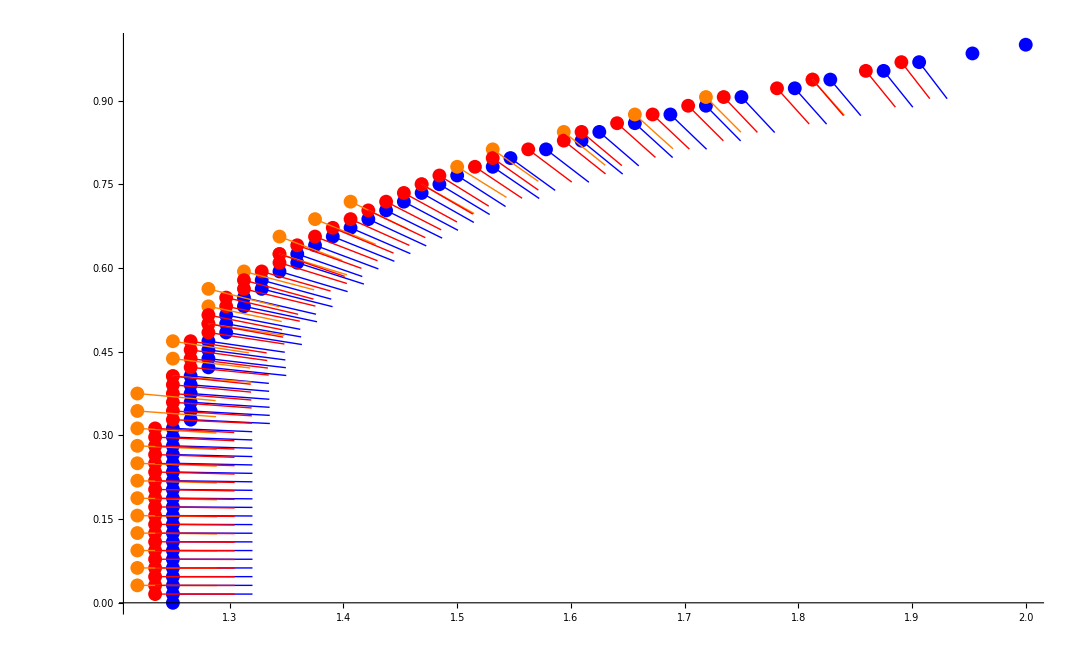

```mathematica
ListPlot[{boundary3,boundary22,boundary33},PlotStyle->{Blue, Orange,Red}, Epilog->{Blue,Arrowheads[0], arrow3,Orange,Arrowheads[0], arrow22, Red,Arrowheads[0], arrow33}]
```